```mathematica
SetDirectory[NotebookDirectory[]];
options={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->22},LabelStyle->Black};
```

```mathematica
Needs["PolygonPlotMarkers`"]

shapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,Scaled[.3]]},ImageSize->30],#]&/@shapes
```

{TripleCross,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Circle}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Sampling from a continuous uniform distribution

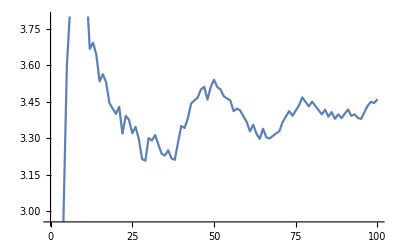

```mathematica
n =100;
data=RandomVariate[DiscreteUniformDistribution[{1,6}],{n}];
fRunningMean[lData__]:=Table[{i,Total[lData[[1;;i]]]/i},{i,1,Length@lData}]
ListLinePlot[fRunningMean[data]]
```

```mathematica
fPlotRunningMean[lData__,aGap_Integer,aActualMean_,aLimits_,aTextPosition_]:=Module[{lRunningMean=fRunningMean[lData]},ParallelTable[Show[ListLinePlot[Thread[{Range@i,lRunningMean[[All,2]][[1;;i]]}],PlotStyle->{Blue,Thickness[0.008]},Evaluate@options,PlotRange->{{0,Length@lRunningMean+1},{aLimits[[1]],aLimits[[2]]}},FrameLabel->{"# shakes","running mean"},ImageSize->600,Epilog->{{Dashed,Thickness[0.005],Line[{{0,aActualMean},{Length@lRunningMean,aActualMean}}]},Style[Text[StringJoin["current value = ",ToString@lData[[i]]],{Length@lData/2,aTextPosition}],Orange,FontSize->22]}],Plot[3.5,{x,0,100},PlotStyle->Directive[Black,Dashed]],ListPlot[Thread[{Range@i,lData[[1;;i]]}],PlotMarkers->Graphics[{FaceForm[Opacity[0.2,Orange]],EdgeForm[Opacity[0.2,Orange]],PolygonMarker["SixPointedStarSlim",Scaled[0.05]]}]],ListPlot[{{i,lData[[i]]}},PlotMarkers->Graphics[{FaceForm[Opacity[1,Orange]],EdgeForm[Opacity[1,Orange]],PolygonMarker["SixPointedStarSlim",Scaled[0.05]]}]]],{i,1,Length@lRunningMean,aGap}]]
```

```mathematica
glist=fPlotRunningMean[data,1,0.5,{0.8,6.2},5.5];
```

```mathematica
ListAnimate[glist]
```

```mathematica
Table[Export[StringJoin["./animations/dice_throwing_",ToString@i,".pdf"],glist[[i]]],{i,1,n,1}];
```